# 傅里叶级数 - 实数到复平面的映射

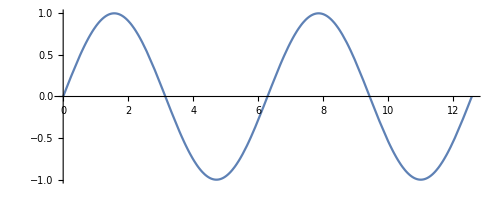

```mathematica
f[x_]:=x+I Sin[x];
ParametricPlot[ReIm[f[x]],{x,0,4π}]
```

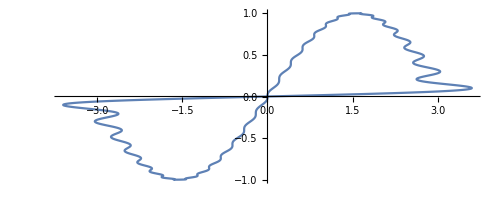

```mathematica
n=30;
cn=Table[1/(2π)Integrate[f[x]Exp[-I k x],{x,-π,π}],{k,-n,n}]
p=Sum[cn[[r]]Exp[(r-n-1)I t],{r,2n+1}];
ParametricPlot[ReIm@p,{t,0,2π}]
```

### 将上面过程包装到函数

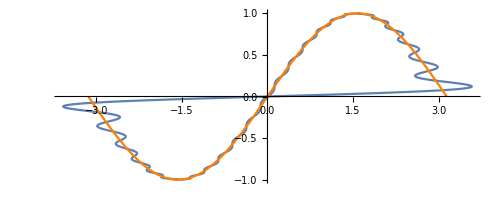

```mathematica
fourierSeriesPlot[f_,n_]:=Block[{cn},cn=Table[1/(2π)Integrate[(x+I f)Exp[-k I x],{x,-π,π}],{k,-n,n}];Show[ParametricPlot[ReIm@Sum[cn[[r+n+1]]Exp[r I t],{r,-n,n}],{t,0,2π}],Plot[f,{x,-π,π},PlotStyle->Orange]]]
fourierSeriesPlot[Sin[x],25]
```

### 使用内置函数计算傅里叶级数

将实函数f当作复平面上的复函数x+I f，再计算其n阶傅里叶级数并绘图

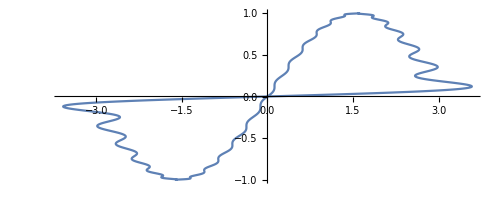

```mathematica
fsPlotComplex[f_,n_]:=ParametricPlot[Evaluate@ReIm@FourierSeries[x+I f,x,n],{x,0,2π}]
fsPlotComplex[Sin[x],25]
```

计算实函数f的傅里叶级数并绘图

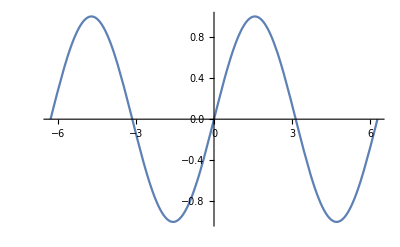

```mathematica
fsPlot[f_,n_]:=Plot[Evaluate@FourierSeries[f,x,6],{x,-2π,2π}]
fsPlot[Sin[x],25]
```

上面第一个是在复数域绘图，第二个是在实数域绘图

### 再看看函数：x/2

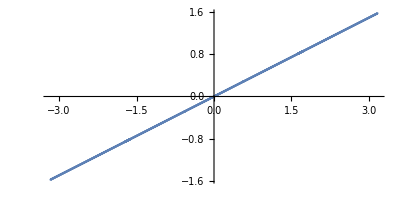

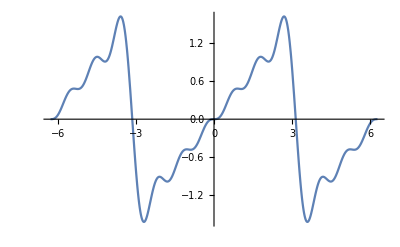

```mathematica
fsPlotComplex[x/2,5]
fsPlot[x/2,5]
```

### 两者彷佛在某个地方表现相反，为什么呢？

其实这再次体现了之前的一个认识，从复数域观察和从实数域观察是从两个垂直的视角观察，
看到的是3D空间的两个投影。

```mathematica
fs=FourierSeries[x/2,x,5];
fsc=FourierSeries[x+I x/2,x,5];
ParametricPlot3D[{{0,Re@fsc,Im@fsc},{x,0,fs},{x,Re@fsc,Im@fsc}},{x,0,2π},RotationAction->"Clip",AxesOrigin->{0,0,0}]
```

-Graphics3D-

从某种角度看，类似与信号的时域和频域的关系，把x当作时间参数。

### 看看其他函数在实数域计算傅里叶级数的图形

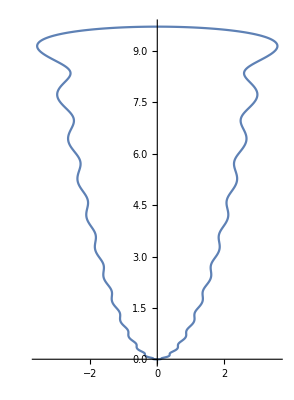

```mathematica
fsPlotComplex[x^2,25]
```

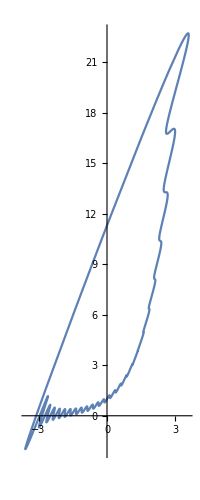

```mathematica
fsPlotComplex[Exp[x],25]
```

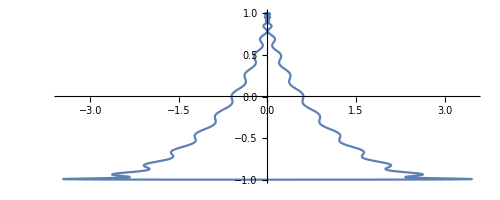

```mathematica
fsPlotComplex[Exp[I x],25]
```

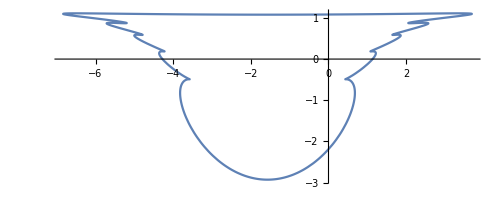

```mathematica
fsPlotComplex[Log[x],10]
```

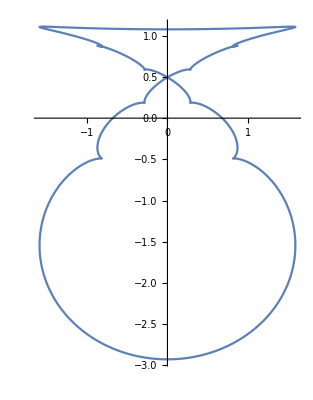

```mathematica
fsPlotComplex[Log[I x],10]
```